```mathematica
pBall = TriangularDistribution[{8.05, 17.09}, 9.17]
```

TriangularDistribution[{8.05,17.09},9.17]

```mathematica
distBall = PDF[pBall, x]
```

Piecewise[{{0.197535 (-8.05+x), 8.05≤x≤9.17}, {0.0279342 (17.09-x), 9.17<x≤17.09}, {0, True}}]

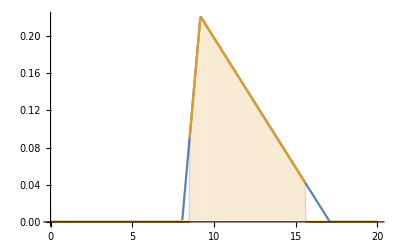

```mathematica
Plot[Evaluate[distBall*{1,Boole[8.5<x<15.6]}],{x,0,20},Filling->{2->Axis}]
```

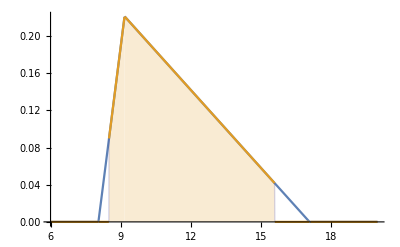

```mathematica
Plot[Evaluate[distBall*{1,Boole[8.5<x<15.6]}],{x,6,20},Filling->{2->Axis}]
```

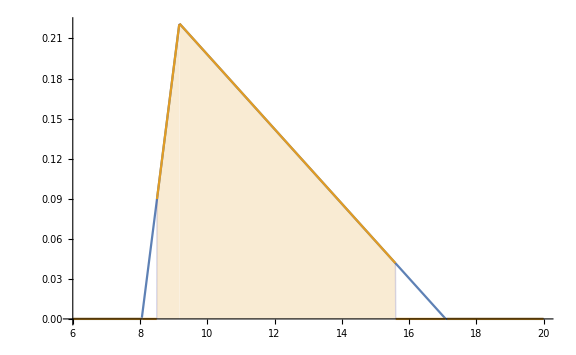

```mathematica
Show[%4,ImageSize->Large]
```

```mathematica
CDF[pBall, 17.09]
```

1.

```mathematica
CDF[pBall, 15.6]
```

0.968992

```mathematica
CDF[pBall, 8.5]
```

0.0200004

```mathematica
0.9689916309108787 - 0.02000039506953219
```

```mathematica
1 - $$E_1\sim Bin(p=1-0.948991;\ N=50)$$
```

```mathematica
1 - 0.948991
```

```mathematica
\
```

```mathematica
binDist1 = BinomialDistribution[50, 0.05100899]
```

BinomialDistribution[50,0.051009]

```mathematica
CDF[binDist1, 2]
```

0.527287

```mathematica
CDF[binDist1, 5]
```

0.958991

```mathematica
binDist2 = BinomialDistribution[100, 0.05100899]
```

BinomialDistribution[100,0.051009]

```mathematica
PDF[binDist1, 3]
```

0.222083

```mathematica
PDF[binDist1, 3] * PDF[binDist2, 0] + PDF[binDist1, 3] * PDF[binDist2, 1] + PDF[binDist1, 3] * PDF[binDist2, 2] + PDF[binDist1, 3] * PDF[binDist2, 3]
```

0.054134

```mathematica
Sum[PDF[binDist1, 3] * PDF[binDist2, i], {i, 0, 3}]
```

0.054134

```mathematica
ScientificForm[0.05413399220822363]
```

5.4134×10^-2

```mathematica
Sum[PDF[binDist1, 4] * PDF[binDist2, i], {i, 0, 2}]
```

0.0154391

```mathematica
Sum[PDF[binDist1, 5] * PDF[binDist2, i], {i, 0, 1}]
```

0.00235399

```mathematica
0.054134+0.0154391+0.00235399
```

0.0719271

```mathematica
Binom[79, 4]*(0.051009)^5*(1 - 0.051009)^(75)
```

6.80599×10^-9 Binom[79,4]

```mathematica
Binom[79,4]
```

Binom[79,4]

```mathematica
Binomial[79, 4] * (0.051009)^5*(1 - 0.051009)^(75)
```

0.010226

```mathematica
Binomial[80 - 1, 5 - 1] * (0.051009)^5*(1 - 0.051009)^(80 - 5)
```

0.010226

```mathematica
Binomial[5 - 1, 5 - 1] * (0.051009)^5*(1 - 0.051009)^(5 - 5)
```

3.4533×10^-7

```mathematica
(Binomial[30, 6] * Binomial[70, 14]) / (Binomial[100, 20])
```

2936300654300/13715194896249

```mathematica
N[2936300654300/13715194896249]
```

0.214091

```mathematica
(Binomial[30, 6] * Binomial[70, 14]) / (Binomial[100, 20]) \\TeXForm
```

Syntax::tsntxi: "(Binomial[30, 6] * Binomial[70, 14])/(Binomial[100, 20]) \\ TeXForm" is incomplete; more input is needed.""

```mathematica
Binomial[9, 0] * (0.051009) * (1 - 0.051009)^9
```

0.0318424

```mathematica
Binomial[10, 1] * (0.051009)^2 * (1 - 0.051009)^9
```

0.0162425

```mathematica
0.03184238968197419 * 0.016242484552878213
```

0.0005172

```mathematica
(5 * (1 - 1-0.051009)) / (1-0.051009)
```

-0.268754

```mathematica
(5 * (1 - (1-0.051009))) / (1-0.051009)
```

0.268754

```mathematica
5 / (1-0.051009)
```

5.26875

```mathematica
1-0.051009
```

0.948991

```mathematica
5 * (1 - 0.948991) / 0.948991
```

0.268754

```mathematica
75 * (1 - 0.948991) / 0.948991
```

4.03131

```mathematica
Sum[(Binomial[30, i] * Binomial[70, 20 - i]) / Binomial[100, 20], {i, 0, 6}]
```

8435940105002/13715194896249

```mathematica
N[8435940105002/13715194896249]
```

0.61508